## Research Tasks Geometry

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## OTHER STUFF

## Apps

### Case 1

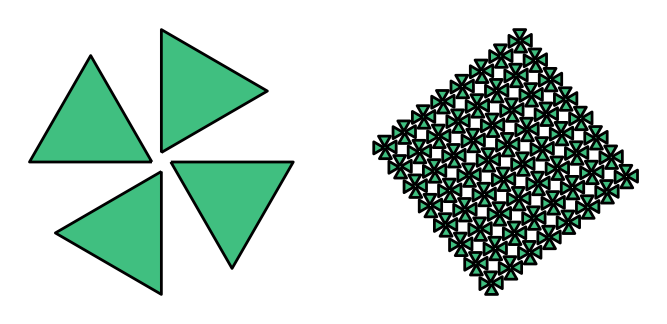

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:=tra3[newGeo[6],{2,1}]
dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}

dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

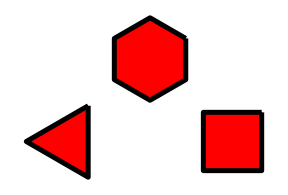

```mathematica
dpoly1:=tra3[newGeo[3],{0,0}]
dpoly2:=tra3[newGeo[4],{4,0}]
dpoly3:=tra3[newGeo[6],{2,2}]
Graphics[{dpoly1,dpoly2,dpoly3}]//toGL
```

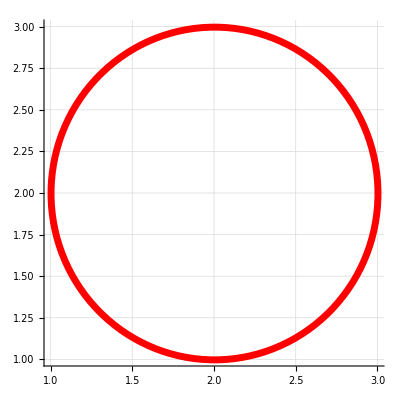

```mathematica
cCircle[{2,2},1]//toGL//gr1
```

### Case 2

```mathematica
cCircle[{5,5},1.5]//toGL
```

{RGBColor[0, 1, 1],Opacity[1],{Thickness[0.0025],Dashing[{2 π,2 π}],Circle[{5,5},1.5]}}

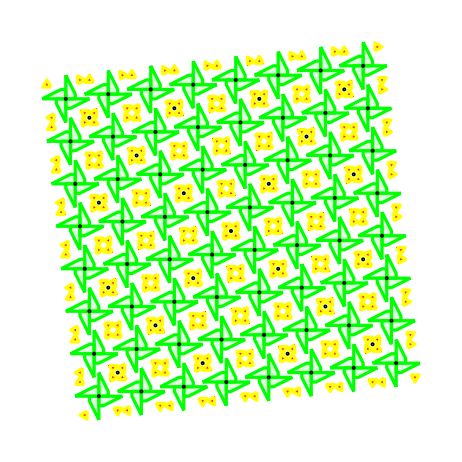

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]

dpolyA:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyB:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
Nest[teil,{dpolyB,dpolyA},4]//toGL//gr
```

### Case 3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},3]
```

```mathematica
dpoly:={{{1,{{0,0},{0.5,0.2},{1,1},{0.2,0.9}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{0.7,1},{0.3,1}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.25,0},{0.5,0.25},{0.5,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
sym4rot[sym4ref[dpoly]]//toGL//gr1
```

-Graphics-

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Case 4 ( IN-DEVELOPMENT )

```mathematica
dpoly0:={{{1,{{0.25,0.0},{0.5,0.0},{0.5,0.75},{0.75,0.75},{0.75,1.0},{0.0,1.0},{0.0,0.75},{0.25,0.75}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyA:={{{1,{{0.5,0},{1,0.5},{1,1},{0.5,0.5},{0,1},{0,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyB:={{{1,{{0,0},{0.5,0},{0,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyC:={{{1,{{0.5,0},{1,0},{1,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={dpolyA,dpolyB,dpolyC}
dpoly//toGL//gr1;
sym4ovr1[dpoly]//toGL//gr1
```

-Graphics-

```mathematica
sym4ovr1[figke_]:=Module[{rotp},
rotp={1,1};
tra3[Scale[
{
figke,
rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],
tra3[figke,{1,1}],
tra3[rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],{-1,1}]
},
.5],{-.5,-.5}]]
```

```mathematica
ind:=Tuples[Composition@@{sym4rot,sym4ref,sym4ovr1},3]
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ind//TableForm
```

sym4rot@*sym4rot@*sym4rot
sym4rot@*sym4rot@*sym4ref
sym4rot@*sym4rot@*sym4ovr1
sym4rot@*sym4ref@*sym4rot
sym4rot@*sym4ref@*sym4ref
sym4rot@*sym4ref@*sym4ovr1
sym4rot@*sym4ovr1@*sym4rot
sym4rot@*sym4ovr1@*sym4ref
sym4rot@*sym4ovr1@*sym4ovr1
sym4ref@*sym4rot@*sym4rot
sym4ref@*sym4rot@*sym4ref
sym4ref@*sym4rot@*sym4ovr1
sym4ref@*sym4ref@*sym4rot
sym4ref@*sym4ref@*sym4ref
sym4ref@*sym4ref@*sym4ovr1
sym4ref@*sym4ovr1@*sym4rot
sym4ref@*sym4ovr1@*sym4ref
sym4ref@*sym4ovr1@*sym4ovr1
sym4ovr1@*sym4rot@*sym4rot
sym4ovr1@*sym4rot@*sym4ref
sym4ovr1@*sym4rot@*sym4ovr1
sym4ovr1@*sym4ref@*sym4rot
sym4ovr1@*sym4ref@*sym4ref
sym4ovr1@*sym4ref@*sym4ovr1
sym4ovr1@*sym4ovr1@*sym4rot
sym4ovr1@*sym4ovr1@*sym4ref
sym4ovr1@*sym4ovr1@*sym4ovr1

## Test Möbius Transformations

```mathematica
FileNameJoin[{$InstallationDirectory,"SystemFiles","Components","AutoCompletionData","Main","OptionValues"}]
```

C:\Program Files\Wolfram Research\Mathematica\12.3.1\SystemFiles\Components\AutoCompletionData\Main\OptionValues

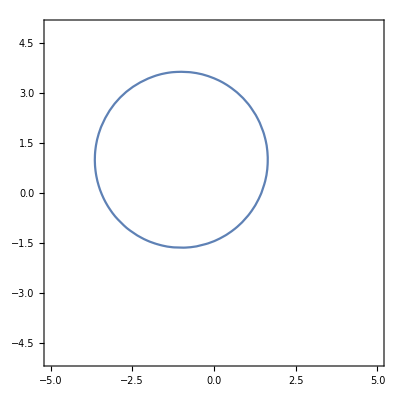

```mathematica
ClearAll[x,y]
ContourPlot[x^2+y^2+2x-2y-5==0,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
(3z Conjugate[z]//ComplexExpand)/.z:>x+I y//Expand
```

```mathematica
z Conjugate[z]/. z-> x+I y
```

(x+ⅈ y) (Conjugate[x]-ⅈ Conjugate[y])

```mathematica
3(x+I y)(x-I y)//Expand
```

3 x^2+3 y^2

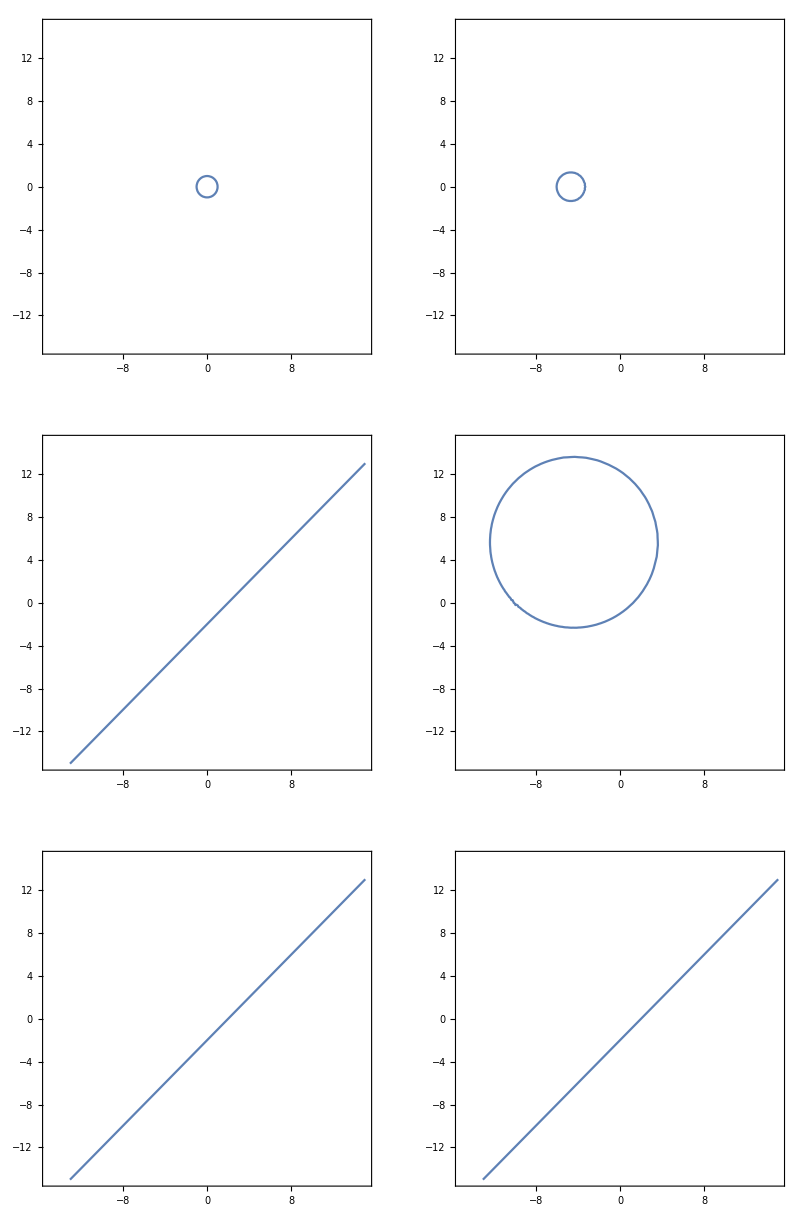

```mathematica
eqn1=ComplexExpand[z Conjugate[z]-1/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn2=ComplexExpand[z Conjugate[z]-1/.z->(0.5z+1)/(1z+4),z]/.{Re[z]->x,Im[z]->y}//FullSimplify;
eqn3=ComplexExpand[Im[z]-Re[z]+2/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn4=ComplexExpand[Im[z]-Re[z]+2/.z->(z+1)/(.1z+1),z]/.{Re[z]->x,Im[z]->y};
eqn5=ComplexExpand[Im[z]-Re[z]+2/.z->(z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn6=ComplexExpand[Im[z]-Re[z]+2/.z->(z+2)/(.1z+1)/.z->(1z-2)/(-.1z+1),z]/.{Re[z]->x,Im[z]->y};

a=15;
GraphicsGrid[{
{
ContourPlot[eqn1==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn2==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn3==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn4==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn5==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn6==0,{x,-a,a},{y,-a,a},Axes->True]
}
}]
```

```mathematica
z Conjugate[z]-1/.z->(1z-5)/(0z+5)//Expand
```

-z/5-Conjugate[z]/5+1/25 z Conjugate[z]

```mathematica
m:={{4,9},{11,25}};
t:={{1,1},{0,1}};
```

```mathematica
m//mf
m.Inverse[t]//mf
m.Inverse[t].Inverse[t]//mf
m.MatrixPower[Inverse[t],5]//mf
```

(4 | 9
11 | 25)

(4 | 5
11 | 14)

(4 | 1
11 | 3)

(4 | -11
11 | -30)

```mathematica
Clear[a,b,c,d]
ma={{a,b},{c,d}};
mt={{1,1},{0,1}};
ms={{0,-1},{1,0}};
mst={{0,-1},{1,1}};
```

```mathematica
mst.ma.Inverse[mst]//mf
```

(-c+d | -c
a-b+c-d | a+c)

```mathematica
mt.{1,0}.Inverse[mt]
```

{1,-1}

```mathematica
maa={{5,2},{-2,3}};
maa={{b+d,b},{-b,d}};
maa1={{a,-c},{c,a+c}};
{mst.maa,maa.mst}
{mst.maa1,maa1.mst}
```

{{{b,-d},{d,b+d}},{{b,-d},{d,b+d}}}

{{{-c,-a-c},{a+c,a}},{{-c,-a-c},{a+c,a}}}

```mathematica
mm={{1,0,1,-1},{0,1,1,0},{1,-1,0,-1},{1,0,1,-1}};
```

```mathematica
MatrixRank[mm]
NullSpace[mm]
RowReduce[mm]
```

2

{{1,0,0,1},{-1,-1,1,0}}

{{1,0,1,-1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}

```mathematica
mm.{-1,-1,1,0}
```

{0,0,0,0}

```mathematica
maa2=a mst+b IdentityMatrix[2];
maa2=a IdentityMatrix[2] + b mst+c Inverse[mst]
mst.maa2//mf
maa2.mst//mf
```

{{a+c,-b+c},{b-c,a+b}}

(-b+c | -a-b
a+b | a+c)

(-b+c | -a-b
a+b | a+c)

```mathematica
mst//mf
Inverse[mst]//mf
```

(0 | -1
1 | 1)

(1 | 1
-1 | 0)

```mathematica
Graphics3D[{Opacity[0.6],Octahedron[],Circumsphere[Octahedron[]]}]
```

-Graphics3D-

## Lines-UZT-1

```mathematica
p1:={0,0};
p2:={3,1};
p3:={1,3};
p4:={4,3};
p5:={-2,3};
Graphics[{
Arrow[{p1,p5}],
Line[{p1,p2}],
HalfLine[{p1,p4}],
Dashed,InfiniteLine[{p1,p3}]
},
AxesOrigin->{0,0},Axes->True,AxesLabel->{"X","Y"},
PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-

```mathematica
tra3cp[figs_,t_]:={figs,figs/.f:pnt:>TranslationTransform[t][f]}
```

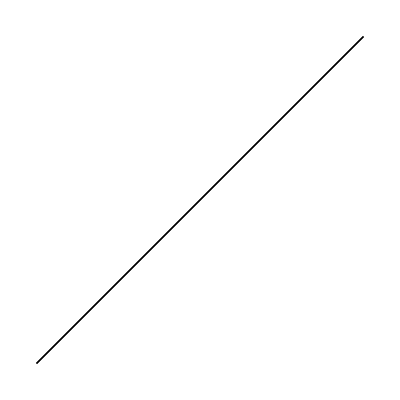

```mathematica
tra3cp[{Line[{{0,0},{1,1}}]},{0,0}]//toGL//Graphics
```

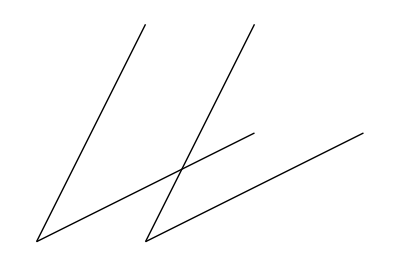

```mathematica
tra3cp[{Line[{{0,0},{4,2}}],Line[{{0,0},{2,4}}]},{-2,0}]//toGL//Graphics
```

```mathematica
trans[figke_]:= Module[{},
{
figke,
tra3cp[figke,{1,0}]
}
]
line:={Line[{{0,0},{4,2}}]}
```

```mathematica
Fold[tra3cp,line,Table[{1,1},{k,1}]]//tf
```

Line[{{0,0},{4,2}}]
Line[{{1,1},{5,3}}]

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,2}]]//tf
```

Line[{{0,0},{4,2}}] | Line[{{1,1},{5,3}}]
Line[{{2,2},{6,4}}] | Line[{{3,3},{7,5}}]

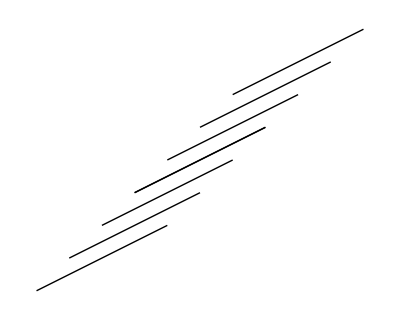

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,3}]]//toGL//Graphics
```

## Lines-UZT-2

```mathematica
Table[ReIm[ⅇ^((k 2 Pi I)/4)],{k,0,3}]//tf
Table[ReIm[ⅇ^((k 2 Pi I)/8)],{k,0,7}]//tf
```

1 | 0
0 | 1
-1 | 0
0 | -1

1 | 0
1/(√2) | 1/(√2)
0 | 1
-1/(√2) | 1/(√2)
-1 | 0
-1/(√2) | -1/(√2)
0 | -1
1/(√2) | -1/(√2)

```mathematica
lines[n_]:=Map[Line[{{0,0},#}]&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
{{{1,{{0,0},#}},{White,1}},{Black,1,.005,2 π,2 π}};
lines[n_]:=Map[{{{1,{{0,0},#}},{Red,1}},{Blue,1,.005,2 π,2 π}}&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
```

```mathematica
GraphicsRow[{
lines[18]//toGL//Graphics
}]
```

-Graphics-

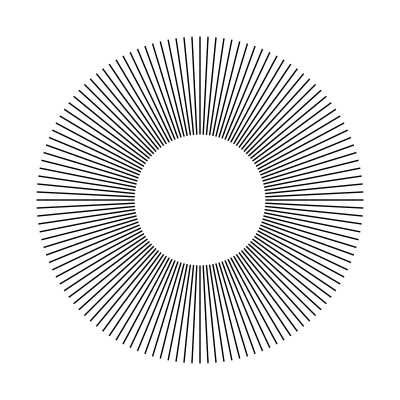

```mathematica
lines2[n_]:=Map[Line[{0.4#[[2]],#[[2]]}]&,Table[{(k+1)/n ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines2[128]//toGL//Graphics
```

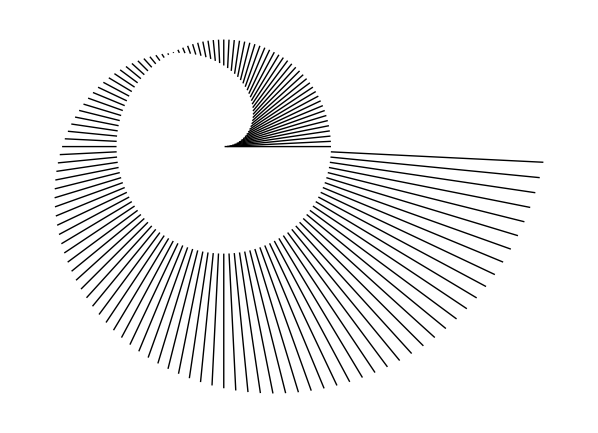

```mathematica
lines3[n_]:=Map[Line[{#[[1]],#[[2]]}]&,Table[{((3k+1)/n)ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines3[128]//toGL//Graphics
```

```mathematica
Integrate[Sin[x] x^2,{x,a,b}]
```

(-2+a^2) Cos[a]-(-2+b^2) Cos[b]-2 a Sin[a]+2 b Sin[b]

## Lines-UZT-3-Definition-for-KickOff

### Scaled

```mathematica
Graphics[{Disk[Scaled[{.25,.25}],1]},Frame->True,PlotRange->{{0,10},{0,10}}]
```

-Graphics-

```mathematica
Graphics[Disk[Scaled[{.50,.50}],10],PlotRange->{{-100,100},{-100,100}},Frame->True,AxesOrigin->{0,0},Axes->True]
```

-Graphics-

### Offset

## OLD-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## tmp-1

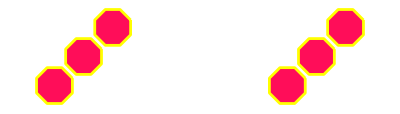

```mathematica
dpolyA:={tra3[newGeo[8,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyA;
dpolyA//toGL;
{dpolyA,tra3[dpolyA,{2,2}]}//toGL ;
{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]}//toGL;
{{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},tra3[{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},{12,0}]}//toGL//gr
```

```mathematica
newGeo[1,Red,{{4,4}}]//toGL
```

newGeo[1,RGBColor[1, 0, 0],{{4,4}}]

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.05],Dashing[{2 π,2 π}]}],Polygon[…]}}//gr
```

-Graphics-

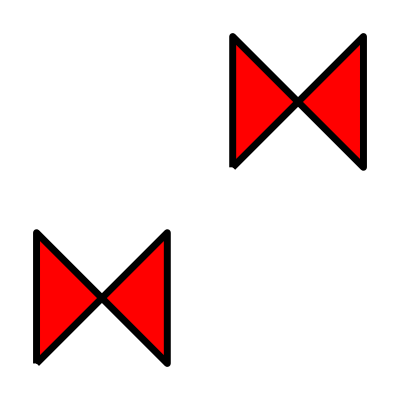

```mathematica
{newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],tra3[newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],{6,6}]}//toGL//gr
```

```mathematica
CoordinateTransformData[]//tf;
CoordinateChartData[]//tf
```

Bipolar
a | Euclidean | 2
BipolarCylindrical
a | Euclidean | 3
Bispherical
a | Euclidean | 3
Cartesian | Euclidean | 1
Cartesian | Euclidean | 2
Cartesian | Euclidean | 3
Cartesian | Euclidean | 4
Cartesian | Euclidean | 5
Cartesian | Euclidean | 6
Cartesian | Euclidean | 7
Cartesian | Euclidean | 8
Cartesian | Euclidean | 9
Cartesian | Euclidean | 10
CircularParabolic | Euclidean | 3
Confocal | 
α | β | Euclidean | 2
Confocal |  | 
α | β | γ | Euclidean | 3
Confocal |  |  | 
α_1 | α_2 | α_3 | α_4 | Euclidean | 4
Confocal |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | Euclidean | 5
Confocal |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | Euclidean | 6
Confocal |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | Euclidean | 7
Confocal |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | Euclidean | 8
Confocal |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | Euclidean | 9
Confocal |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | Euclidean | 10
Confocal |  |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | α_11 | Euclidean | 11
ConfocalParaboloidal | 
α | β | Euclidean | 3
Conical | 
b | c | Euclidean | 3
Cylindrical | Euclidean | 3
Elliptic
a | Euclidean | 2
EllipticCylindrical
a | Euclidean | 3
Polar | Euclidean | 2
Hyperspherical | Euclidean | 3
Hyperspherical | Euclidean | 4
Hyperspherical | Euclidean | 5
Hyperspherical | Euclidean | 6
Hyperspherical | Euclidean | 7
Hyperspherical | Euclidean | 8
Hyperspherical | Euclidean | 9
Hyperspherical | Euclidean | 10
Hyperspherical | Euclidean | 11
OblateSpheroidal
a | Euclidean | 3
ParabolicCylindrical | Euclidean | 3
PlanarParabolic | Euclidean | 2
ProlateSpheroidal
a | Euclidean | 3
Spherical | Euclidean | 3
Toroidal
a | Euclidean | 3
Standard | Sphere
R | 1
Standard | Sphere
R | 2
Standard | Sphere
R | 3
Standard | Sphere
R | 4
Standard | Sphere
R | 5
Standard | Sphere
R | 6
Standard | Sphere
R | 7
Standard | Sphere
R | 8
Standard | Sphere
R | 9
Standard | Sphere
R | 10
Stereographic | Sphere
R | 1
Stereographic | Sphere
R | 2
Stereographic | Sphere
R | 3
Stereographic | Sphere
R | 4
Stereographic | Sphere
R | 5
Stereographic | Sphere
R | 6
Stereographic | Sphere
R | 7
Stereographic | Sphere
R | 8
Stereographic | Sphere
R | 9
Stereographic | Sphere
R | 10

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1,-1}]
CoordinateTransform[{"Polar"->"Cartesian",2},{√2,-π/4}]
```

{√2,-π/4}

{1,-1}

```mathematica
FromPolarCoordinates[ToPolarCoordinates[{1/(√2),1/(√2)}]]
FromSphericalCoordinates[ToSphericalCoordinates[{{x,y,z},{1,0,0}}]]
```

{1/(√2),1/(√2)}

{{x,y,z},{1,0,0}}

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1/√2,-1/√2}]
```

{1,-π/4}

```mathematica
1/((1/√2)+I(1/√2))
```

(1-ⅈ)/(√2)

```mathematica
FromPolarCoordinates[{R,θ}]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]//FullSimplify
```

{R Cos[θ],R Sin[θ]}

{√(R^2 Cos[θ]^2+R^2 Sin[θ]^2),ArcTan[R Cos[θ],R Sin[θ]]}

{√(R^2),ArcTan[R Cos[θ],R Sin[θ]]}

```mathematica
D[Exp[x],x]==Exp[x]
```

True

```mathematica
168-(18+17+15+13+12+15+14)-4
```

60

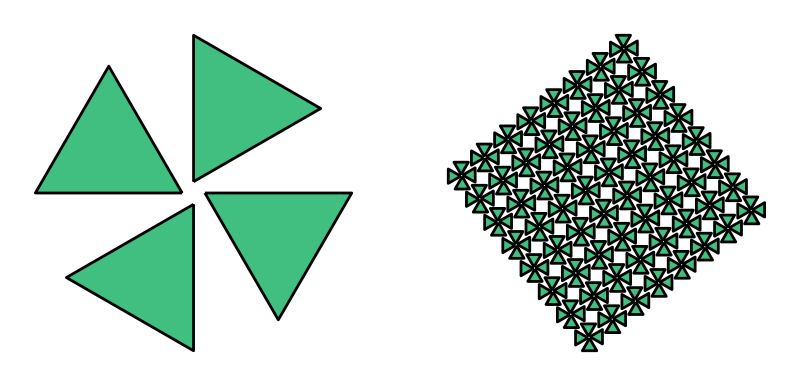

```mathematica
dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

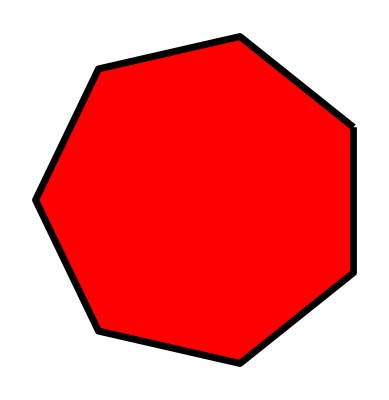

```mathematica
newGeo[7]//toGL//gr
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

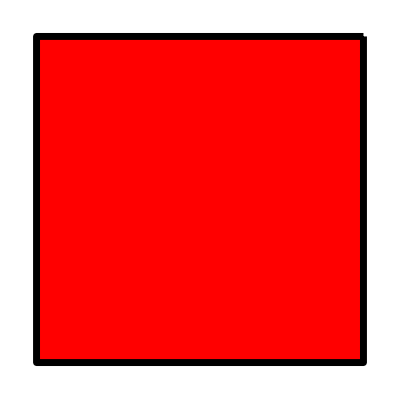

```mathematica
nGonAtEdge3[newGeo[4],{3,4}]//toGL//gr
```

## notes

## tmp-1

```mathematica
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL
```

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Polygon[…]}}

```mathematica
EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}]
```

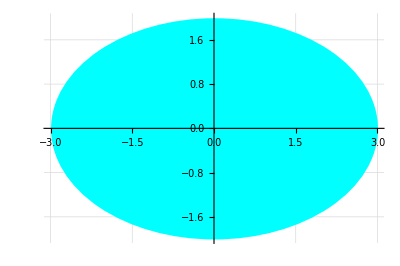

```mathematica
{Cyan,Ellipsoid[{0,0},{3,2}]}//gr1
```

```mathematica
EntityValue[
Entity["Country","Netherlands"],
EntityProperty["Country","Population"]
]
```

17591475 people

```mathematica
EntityValue[
Entity["Country","China"],
EntityProperty["Country","Population"]
]
```

1425700000 people

```mathematica
EntityValue[]
```

{AdministrativeDivision,Aircraft,Airline,Airport,AirportType,Alphabet,AmusementPark,AmusementParkRide,AmusementParkType,AnatomicalConceptIdentifier,AnatomicalFunctionalConcept,AnatomicalSpatialConcept,AnatomicalStructure,AnatomicalTemporalConcept,AnimalAnatomicalStructure,AnimalCoatColorAndPattern,AnimalEggColor,AnimalFeatherColor,AnimalSkinColor,AnimalUse,ArchitecturalStyle,Artwork,AstronomicalObservatory,AstronomicalRadioSource,AtmosphericLayer,AtomicLevel,AtomicLine,BasicFoodGroup,Beach,BioSequenceType,BoardGame,Book,Bridge,BridgeType,BroadcastStation,BroadcastStationClassification,Building,CalculusResult,Canal,Castle,CatBreed,CattleBreed,Cave,Cemetery,Character,Chemical,City,ClimateType,Cloud,CognitiveTask,Color,ColorSet,Comet,Company,ComputationalComplexityClass,Concept,Constellation,ConstructionMaterial,ContinuedFraction,ContinuedFractionResult,ContinuedFractionSource,Country,CrystalFamily,CrystallographicSpaceGroup,CrystalSystem,CurrencyDenomination,CurrencyDenominationType,Dam,DeepSpaceProbe,Desert,Digimon,Dinosaur,Disease,DisplayFormat,DistrictCourt,DogBreed,EarthImpact,Earthquake,EclipseType,ElectricalOutlet,Element,Emotion,EthnicGroup,Exoplanet,FamousChemistryProblem,FamousGem,FamousMathGame,FamousMathProblem,FamousPhysicsProblem,FAOConservationStatus,FictionalCharacter,FictionalPlace,FictionalSpecies,FileFormat,Financial,FiniteGroup,Flight,FlightStatus,Food,FoodAge,FoodAlcoholLabel,FoodBeefGrade,FoodBoneContent,FoodBrandName,FoodCaffeineLabel,FoodCalorieLabel,FoodComposition,FoodConcentration,FoodCrustType,FoodCulture,FoodDataSource,FoodFatLabel,FoodFatType,FoodFiberLabel,FoodFlavor,FoodGeometryType,FoodGlutenContent,FoodIntendedUse,FoodIronLabel,FoodLocation,FoodMaltType,FoodManufacturer,FoodMeatCut,FoodMeatQuality,FoodMoistureLevel,FoodNutritionalSupplement,FoodNutritionalSupplementNotAdded,FoodPackaging,FoodPart,FoodPattyCount,FoodPeelingType,FoodPreparation,FoodProcessingType,FoodSeafoodVariety,FoodSeedContent,FoodServingType,FoodShape,FoodSize,FoodSkinContent,FoodSodiumLabel,FoodState,FoodStorageType,FoodSubBrandName,FoodSugarLabel,FoodSugarType,FoodTexture,FoodTrimmingLevel,FoodType,FoodTypeGroup,FoodVariety,FoodVegetablePart,FoodYeastType,Forest,FrequencyAllocation,FunctionalAnalysisSource,FunctionSpace,Galaxy,Gender,Gene,GeneticTranslationTable,GeographicRegion,GeologicalLayer,GeologicalPeriod,GeometricScene,GivenName,Glacier,GlobalClimateData,GoatBreed,GrammaticalUnit,Graph,HistoricalCountry,HistoricalEvent,HistoricalPeriod,HistoricalSite,HorseBreed,HorseBreedConservationStatus,HorseCoatColorAndPattern,HorseType,HorseUse,ICDNine,ICDTen,Icon,IntegerSequence,InternetDomain,IPAddress,Island,ISO15924Group,Isotope,Knot,Lake,Lamina,Language,LanguageLocale,Laser,Lattice,LatticeSystem,LibraryBranch,LibrarySystem,LightColor,LunarInteriorLayer,MannedSpaceMission,MathematicalFunction,MathWorld,MatterPhase,MeasurementDevice,MedicalTest,MeteorShower,MetropolitanArea,MilitaryConflict,MilitaryConflictType,MilitaryFacilityType,Mine,Mineral,MinorPlanet,MoonPhase,Mountain,Movie,MPAARating,Museum,MusicAct,MusicAlbum,MusicAlbumRelease,MusicAlbumType,MusicalInstrument,MusicWork,MusicWorkRecording,MusicWorkRendition,Mythology,NaturalHazard,NaturalResource,NCBITranslationTableVersion,Nebula,Neighborhood,NetworkService,Neuron,NonperiodicTiling,NotableComputer,NuclearExplosion,NuclearExplosionType,NuclearReactor,NuclearReactorType,NuclearTestSite,Nutrient,ObjectStatus,Ocean,OilField,OperatingStatus,OrganizationType,Park,Particle,ParticleAccelerator,ParticulateMatter,Periodical,PeriodicTiling,Person,PersonTitle,PhysicalActivity,PhysicalConstant,PhysicalEffect,PhysicalQuantity,PhysicalSystem,PigBreed,PigeonBreed,PilatesExercise,PlaneCurve,Planet,PlanetaryMoon,Plant,Pokemon,PokemonAbilities,PokemonGeneration,PokemonPokedexColor,PokemonType,Polyhedron,PopularCurve,PoultryBreed,PoultryBreedConservationStatus,PreservationStatus,PrivateSchool,ProgrammingLanguage,Protein,PublicSchool,Pulsar,Reef,Religion,ReserveLand,RiemannHypothesisFormulation,River,Rocket,RocketFunction,Satellite,SchoolDistrict,SheepBreed,Ship,Shipwreck,SkinType,SNP,SolarSystemFeature,Solid,Sound,Source,SpaceCurve,Species,Sport,SportMatch,SportObject,Stadium,Star,StarCluster,StatisticalGroup,StormType,Supernova,SupernovaType,Surface,Surname,SystemModel,TaxonomicRank,TerrainType,TidalConstituent,TideStation,TimeZone,TopLevelDomain,TopologicalSpaceType,Transparency,TropicalStorm,Tunnel,UnderseaFeature,University,USCongressionalDistrict,USDAEggSize,USDAFoodGroup,VisualArtsArtForm,VisualArtsArtGenre,Volcano,Waterfall,WeatherStation,WeightTrainingExercise,WolframDemonstration,WolframLanguageSymbol,Word,WritingDirection,WritingScript,WritingScriptBaseline,WritingScriptLigature,WritingScriptStatus,WritingScriptType,WritingScriptWhiteSpace,YogaPose,YogaPosition,YogaProp,YogaSequence,ZIPCode}

```mathematica
EntityProperties["MusicAlbum"]
```

{label,tracklist,number of discs,number of songs,canonical release,release date,runtime,entity type list,image,artist,type,name,releases}

```mathematica
EntityValue[
Entity["MusicAlbum","Revolver"],
EntityProperty["MusicAlbum","artist"]
]
```

Missing[UnknownEntity,{MusicAlbum,Revolver}]

```mathematica
(168)-(15+11+8+2)//N
```

132.

```mathematica
ClearAll[gCircle]
gCircle[cntr_,r_]:=newGeo[{2,{ReIm[N[cntr]],ReIm[N[cntr+r]]}}]
gCircle[cntr_]:=gCircle[cntr,1]
gCircle[]:=gCircle[0]
```

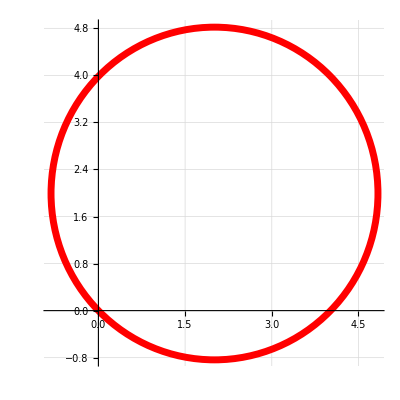

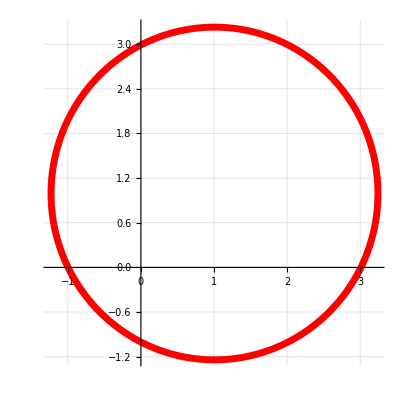

```mathematica
{gCircle[4-2I,4],tra3[gCircle[4-2I,4],{5,5}]}//toGL//gr2;
gCircle[2+2I,2 √2]//toGL//gr1
sca3[gCircle[2+2I,2 √2],{0.5,{2,2}}]//toGL//gr1
```

```mathematica
eqn=2x-y+1==0
```

1+2 x-y==0

```mathematica
eqn//FullForm
eqn[[1,2,1]]
eqn[[1,3,1]]
```

Equal[Plus[1,Times[2,x],Times[-1,y]],0]

2

-1

```mathematica
ClearAll[gCircle]
gCircle[cntr:pnt,r_]:=newGeo[{2,{cntr,{cntr[[1]],cntr[[2]]+r}}}]
gCircle[cntr:pnt]:=gCircle[cntr,1]
gCircle[cntr_,r_]:=newGeo[{2,{ReIm[N[cntr]],ReIm[N[cntr+r]]}}]
gCircle[cntr_]:=gCircle[cntr,1]
gCircle[]:=gCircle[0]
```

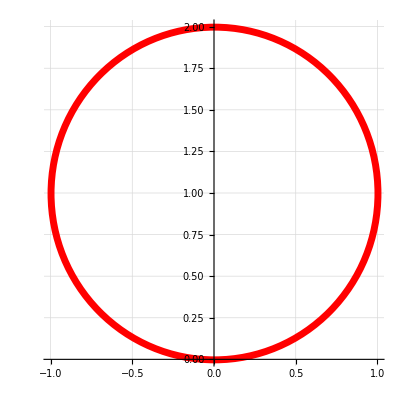

-Graphics-

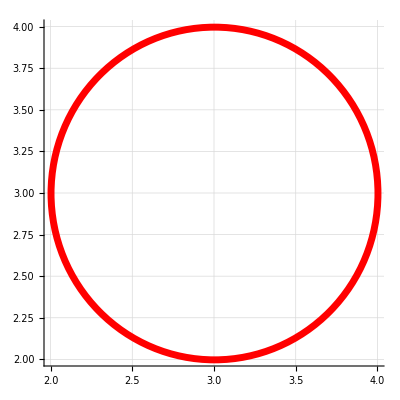

```mathematica
gCircle[I]//toGL//gr1
gCircle[{0,1},1]//toGL//gr1
gCircle[{3,3}]//toGL//gr1
```

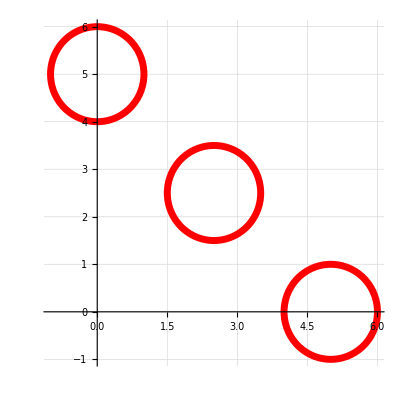

```mathematica
{gCircle[5],gCircle[2.5+2.5I],gCircle[5I]}//toGL//gr1
```

```mathematica
IntegerName[77784 * 1000000000, "Dutch"]
```

zevenenzeventig biljoen zevenhonderdvierentachtig miljard

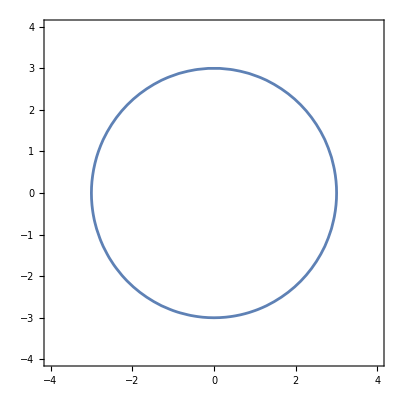

```mathematica
ContourPlot[Abs[x+ⅈ y]^2==9,{x,-4,4},{y,-4,4}]
```

```mathematica
|
```

```mathematica
Abs[z]^2==1/. z:>x+ I y
```

Abs[x+ⅈ y]^2==1

```mathematica
eqn=z+1/.z:>x+ I y;
ContourPlot[eqn==0,{x,-4,4},{y,-4,4}]
```

-Graphics-

```mathematica
eqn
```

1+x+ⅈ y

```mathematica
Refine[z^4/.z:>x+I y //Expand//ReIm,{Element[x,Reals],Element[y,Reals]}]
```

{x^4-6 x^2 y^2+y^4,4 x^3 y-4 x y^3}

```mathematica
ComplexExpand[z^4/.z:>x+I y]/.{Re[z]:>x,Im[z]:>y}/.{Re[z]:>x,Im[z]:>y}
```

x^4-6 x^2 y^2+y^4+ⅈ (4 x^3 y-4 x y^3)

```mathematica
ComplexExpand[z^4/.z:>x+I y]
```

x^4-6 x^2 y^2+y^4+ⅈ (4 x^3 y-4 x y^3)

## tmp-2

```mathematica
A x + B y + C /.{x:>1/2(z+Conjugate[z]),y:>(1/2 I) (z - Conjugate[z])}//Simplify
```

C+1/2 ⅈ B (z-Conjugate[z])+1/2 A (z+Conjugate[z])

```mathematica
eqn=1 x + 2 y + 3 /.{x:>1/2(z+Conjugate[z]),y:>(1/2 I) (z - Conjugate[z])}//Simplify
```

1/2 (6+(1+2 ⅈ) z+(1-2 ⅈ) Conjugate[z])

```mathematica
eqn
```

1/2 (6+(1+2 ⅈ) z+(1-2 ⅈ) Conjugate[z])

```mathematica
eqn=1 x + 2 y + 3 /.{x:>1/2(z+Conjugate[z]),y:>(1/2 I) (z - Conjugate[z])}//Simplify
```

1/2 (6+(1+2 ⅈ) z+(1-2 ⅈ) Conjugate[z])

```mathematica
Refine[eqn=eqn/.{z:>x + I y},{Element[x,Reals],Element[y,Reals]}]//Simplify
```

3+x-2 y

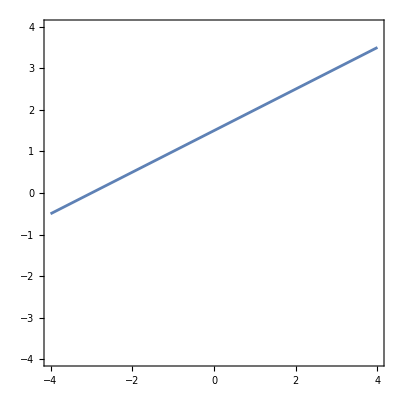

```mathematica
ContourPlot[eqn==0,{x,-4,4},{y,-4,4}]
```

## tmp-3

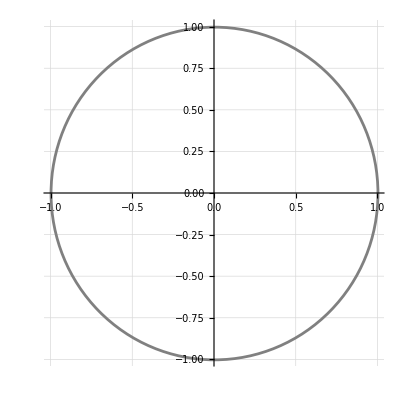

```mathematica
gCircle[Thickness->0.005,Color->Gray]//toGL//gr1
```

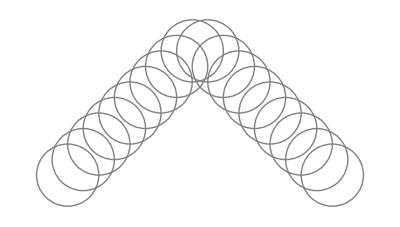

```mathematica
Table[gCircle[{k,If[k<=10,k,11-Mod[k,10]]},2,Color->Gray,Thickness->0.0025],{k,2,19}]//toGL//gr
```

## tmp-4-movie_protocol

```mathematica
(*
Table[gLine[{k,If[k<=10,k,11-Mod[k,10]]},Color->Cyan,Thickness->0.0025],{k,2,19}]//toGL//gr
 f[x_,y_]:=Table[gLine[{x,y},pGon[128][[k]],Color->Gray,Thickness->0.0025],{k,1,128}]//toGL//gr
f[-0.5,-0.5]
gAnimation=ConstantArray[0,101]
Table[{k,k},{k,-0.5,0.5,0.01}]//Length
For[k=1,k<=101,k++,gAnimation[[k]]=f[-0.51+ k/100,-0.51+ k/100]]
Export["movie.avi",gAnimation]
*)
```

## tmp-5

```mathematica
gCircle[]//toGL
```

{RGBColor[1, 0, 0],Opacity[1],{Thickness[0.0125],Dashing[{2 π,2 π}],Circle[{0.,0},1.]}}

```mathematica
{{2,{{0.,0},{1.,0}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}
```

{{2,{{0.,0},{1.,0}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

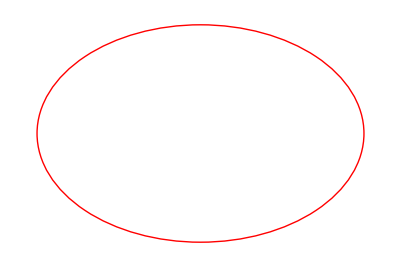

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{Thickness[0.0025],Dashing[{2 π,12π}],Circle[{0.,0},{12.,8}]}}//gr
```

```mathematica
Options[gCircle]
```

{Color→RGBColor[1, 0, 0],Opacity→1,Thickness→0.0125,Dashing→{2 π,2 π}}

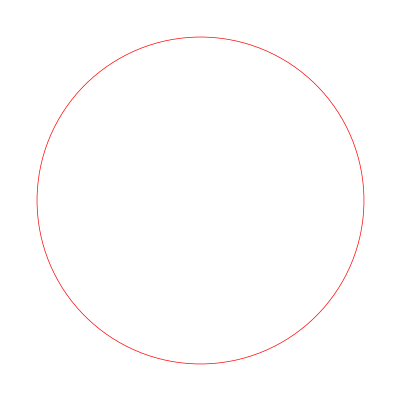

```mathematica
gCircle[Thickness->0.00125]//toGL//gr
```